# PBH constraints

```mathematica
(*Please download the notebook and all the csv data to the same folder, and run the following to set the directory.*)
SetDirectory[NotebookDirectory[]];
```

## Subaru-HSC

### Null detection exclusive curves

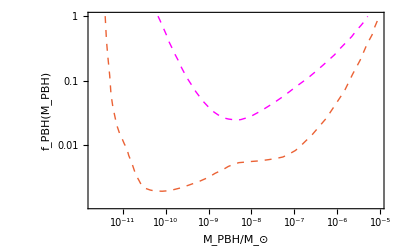

```mathematica
(*Subaru-HSC 2017 constraint: 1701.02151*)
HSC=Import["SubaruHSC.csv"];
hsc=ListPlot[HSC,Joined->True,Frame->True,Filling->Top,PlotStyle->Blue,FrameLabel->{"log_10(M_PBH/M_⊙)","log_10(f_PBH)"}];
HSC2=10^HSC;
hsc2=ListLogLogPlot[HSC2,Joined->True,Frame->True,Filling->None,PlotStyle->{Dashed,Thick,ColorData[97,4]},
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}];
(*SubaruHSC null result from 2602.05840.*)
SubaruNull=Import["SubaruNull.csv"];
subarunull=ListLogLogPlot[SubaruNull,Joined->True,Frame->True,Filling->None,PlotStyle->{Dashed,Thick,Magenta},
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}];
Show[hsc2,subarunull]
```

### Subaru-HSC suggested PBH from all the 12 events

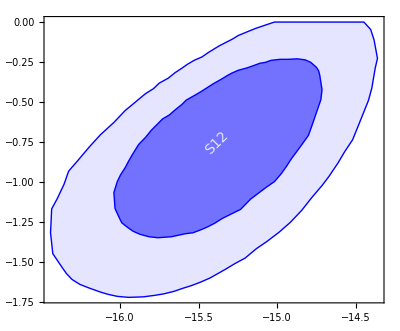

```mathematica
S12B=Import["S12B.csv","CSV"];
pts=Cases[S12B,{x_?NumericQ,y_?NumericQ}:>{N[x],N[y]},Infinity];
logPts1=Log/@pts;
center1={Mean[logPts1[[All,1]]],Mean[logPts1[[All,2]]]};
ordered=SortBy[logPts1,ArcTan[#[[1]]-center1[[1]],#[[2]]-center1[[2]]]&];
polyS12B=Polygon@Append[ordered,First[ordered]];
s12b=Graphics[{{Opacity[0.10],Blue,polyS12B},{Blue,Thick,Line[polyS12B[[1]]]}}];
S12A=Import["S12A.csv","CSV"];
pts2=Cases[S12A,{x_?NumericQ,y_?NumericQ}:>{N[x],N[y]},Infinity];
logPts2=Log/@pts2;
center2={Mean[logPts2[[All,1]]],Mean[logPts2[[All,2]]]};
ordered=SortBy[logPts2,ArcTan[#[[1]]-center2[[1]],#[[2]]-center2[[2]]]&];
polyS12A=Polygon@Append[ordered,First[ordered]];
s12a=Graphics[{{Opacity[0.50],Blue,polyS12A},{Blue,Line[polyS12A[[1]]]},Text[Rotate[Style["S12",FontFamily->"Times",FontSize->14,White],45 Degree],center2]}];
s12=Show[s12a,s12b,Frame->True]
```

```mathematica
10^{center1,center2}
```

{{3.35571×10^-16,0.120793},{4.10561×10^-16,0.175772}}

### Subaru-HSC suggested PBH from all 4 secured events

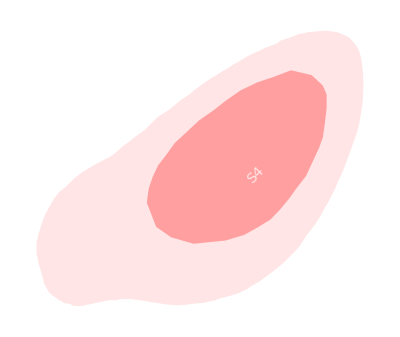

```mathematica
S4B=Import["S4B.csv","CSV"];
pts=Cases[S4B,{x_?NumericQ,y_?NumericQ}:>{N[x],N[y]},Infinity];
logPts=Log/@pts;
center={Mean[logPts[[All,1]]],Mean[logPts[[All,2]]]};
ordered=SortBy[logPts,ArcTan[#[[1]]-center[[1]],#[[2]]-center[[2]]]&];
polyS4B=Polygon@Append[ordered,First[ordered]];
s4b=Graphics[{{Opacity[0.10],Red,polyS4B}}];
S4A=Import["S4A.csv","CSV"];
pts2=Cases[S4A,{x_?NumericQ,y_?NumericQ}:>{N[x],N[y]},Infinity];
logPts=Log/@pts2;
center={Mean[logPts[[All,1]]],Mean[logPts[[All,2]]]};
ordered=SortBy[logPts,ArcTan[#[[1]]-center[[1]],#[[2]]-center[[2]]]&];
polyS4A=Polygon@Append[ordered,First[ordered]];
s4a=Graphics[{{Opacity[0.30],Red,polyS4A},Text[Rotate[Style["S4",FontFamily->"Times",FontSize->14,White],45 Degree],center+{0.15,-0.2}]}];
s4=Show[s4a,s4b]
```

## OGLE

### Null detection

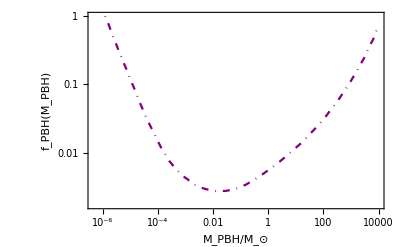

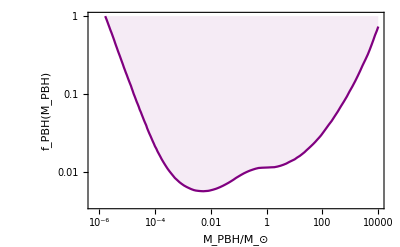

```mathematica
(*OGLE 2024 constraints from 2403.02386.*)
OGLE=Import["OGLE2024.csv"];
ogle=ListPlot[OGLE,Joined->True,Frame->True,Filling->Top,PlotStyle->Cyan];
OGLE2=10^OGLE;
OGLErelax=Import["OGLErelax.csv"];
ogle1=ListLogLogPlot[OGLE2,Joined->True,Frame->True,PlotStyle->{Purple,DotDashed},GridLines->Automatic,
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}]
oglerelax=ListLogLogPlot[OGLErelax,Joined->True,Frame->True,Filling->Top,FillingStyle->{Directive[Purple,Opacity[0.08]]},PlotStyle->Purple,GridLines->Automatic,
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}]
```

### Explain OGLE 6 events by planet-mass PBHs

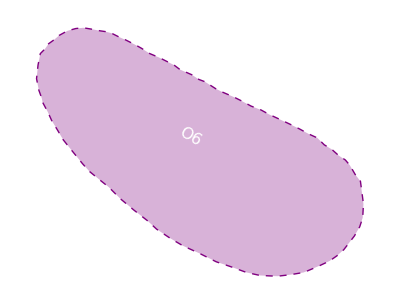

```mathematica
(*The contour is a combination of OGLE 6 events (1707.07634) and the Subaru-HSC (1701.02151) result, given by 1901.07120.*)
contourFile2="OGLEevent.csv";
raw2=Import[contourFile2,"CSV"];
pts2=Cases[raw2,{x_?NumericQ,y_?NumericQ}:>{N[x],N[y]},Infinity];
logPts=Log/@pts2;
center={Mean[logPts[[All,1]]],Mean[logPts[[All,2]]]};
ordered=SortBy[logPts,ArcTan[#[[1]]-center[[1]],#[[2]]-center[[2]]]&];
poly5=Polygon@Append[ordered,First[ordered]];
ogle2=Graphics[{{Opacity[0.30],Purple,poly5},{Purple,Dashed,Thick,Line[poly5[[1]]],Text[Rotate[Style["O6",FontFamily->"Times",FontSize->16,White],-30 Degree],center]}}]
```

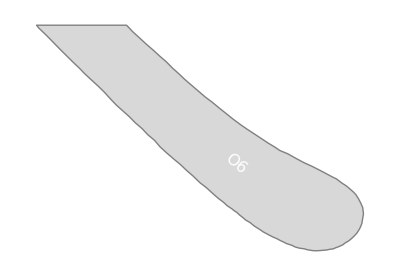

```mathematica
(*The contour used OGLE 6 events (1707.07634) only, also given by 1901.07120. 
Note: As Subaru-HSC already observed ultra-short timescale microlensing events in 2602.05840, the contour above (O6) can not co-exist with the Subaru-HSC contours S12 and S4. *)
contourFile3="ogle2.csv";
raw3=Import[contourFile3,"CSV"];
pts3=Cases[raw3,{x_?NumericQ,y_?NumericQ}:>{N[x],N[y]},Infinity];
logPts=Log/@pts3;
center={Mean[logPts[[All,1]]],Mean[logPts[[All,2]]]};
ordered=SortBy[logPts,ArcTan[#[[1]]-center[[1]],#[[2]]-center[[2]]]&];
poly7=Polygon@Append[ordered,First[ordered]];
ogle3=Graphics[{{Opacity[0.30],Gray,poly7},{Gray,Thick,Line[poly7[[1]]],Text[Rotate[Style["O6",FontFamily->"Times",FontSize->16,White],-40 Degree],center]}}]
```

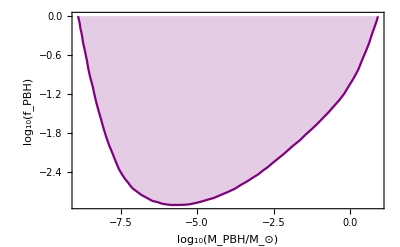

```mathematica
(*This constraint is from OGLE high cadence 2024, 2410.06251. This is in contradiction with Subaru-HSC 2026 result, so we will not use it.*)
OGLEIVh=Import["OGLE-IV-high-cadence.csv"];
OGLEh=ListPlot[OGLEIVh,Joined->True,Frame->True,Filling->Top,PlotStyle->Purple,FrameLabel->{"log_10(M_PBH/M_⊙)","log_10(f_PBH)"}]
```

## CMB accretion

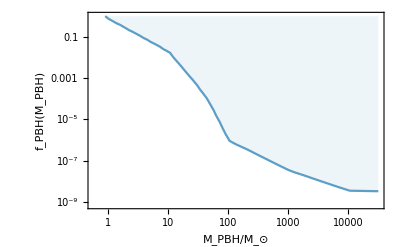

```mathematica
(*CMB accretion from 2002.10771*)
DISK=Import["planckdisk.csv"];
disk=ListPlot[DISK,Frame->True,Filling->Top,PlotStyle->Gray,Joined->True];
DISK2=10^DISK;
disk2=ListLogLogPlot[DISK2,Joined->True,Frame->True,Filling->Top,FillingStyle->Directive[ColorData[97,7],Opacity[0.1]],PlotStyle->
{ColorData[97,7]},
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}]
```

## GW direct detection constraints

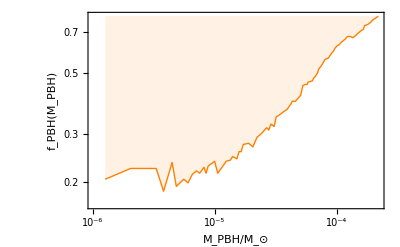

```mathematica
(*LIGO asymmetric merger constraint from 2511.19911.*)
LIGOA=Import["LIGOasym.csv"];
ligoasym=ListLogLogPlot[LIGOA,Joined->True,Frame->True,Filling->Top,FillingStyle->{Directive[Orange,Opacity[0.1]]},PlotStyle->{Orange,Thick},
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}]
```

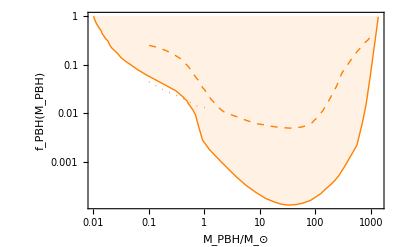

```mathematica
(*LIGO SGWB constraint from 2412.18318, with Subscript[R, cluster]=400.*)
LIGOSGWB=Import["LIGOSGWB.csv"];
ligosgwb=ListLogLogPlot[LIGOSGWB,Joined->True,Frame->True,Filling->None,PlotStyle->{Orange,Thick,Dashed},
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}];
(*LIGO merger constraint from 2405.05732.*)
LIGOmerger=Import["LIGOmerger.csv"];
ligomerger=ListLogLogPlot[LIGOmerger,Joined->True,Frame->True,Filling->Top,FillingStyle->{Directive[Orange,Opacity[0.1]]},PlotStyle->{Orange,Thick},
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}];
(*LIGO direct search for sub-solar mass PBH, from 2602.12115.*)
LIGOsubsolar=Import["LIGOsubsolar.csv"];
ligosubsolar=ListLogLogPlot[LIGOsubsolar,Joined->True,Frame->True,Filling->None,PlotStyle->{Orange,Thick,Dotted},PlotRange->{Automatic,{0.01,1}},
FrameLabel->{"M_PBH/M_⊙","f_PBH(M_PBH)"}];
Show[ligosgwb,ligomerger,ligosubsolar,PlotRange->All]
```

## EROS

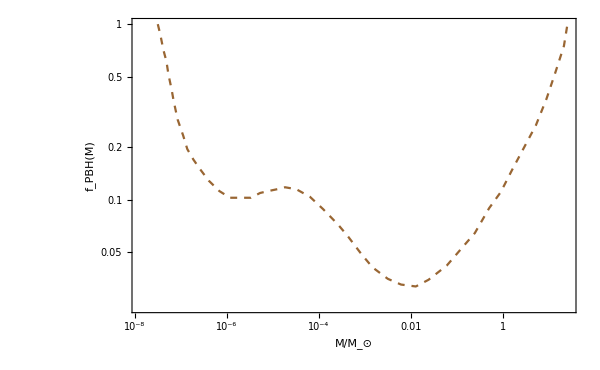

```mathematica
(*EROS is an early microlensing experiments. The curve is from astro-ph/0607207. We also write all the settings of the frame here.*)
EROS=Import["EROS.csv"];
EROS2=10^EROS;
eros3=ListLogLogPlot[EROS2,Joined->True,Frame->True,PlotStyle->{Brown,Dashed},FrameLabel->{"M/M_⊙","f_PBH(M)","<M>/M_⊙",None},LabelStyle->{Black},BaseStyle->{FontFamily->"Times",FontSize->16},FrameStyle->FontFamily->"Times",Axes->False,GridLines->Automatic,PlotTheme->"Scientific",ImageSize->600]
```

```mathematica
(*Customize legend. Add if needed.*)
shadowbox5[legend_]:=Graphics[{{Gray,Rectangle[{0.03,-0.03},{0.53,0.48}]},{White,EdgeForm[Gray],Rectangle[{0,0},{0.50,0.51}]},Inset[legend,{0.25,0.25},Center]},ImageSize->125];
pbhlegend5=SwatchLegend[{Red,Blue,Purple,Cyan,Green,Gray},{"EG/GC γ-ray","Subaru HSC","OGLE-IV HC","OGLE-III+IV","EROS/MACHO","Planck(disk)"},LegendMarkers->Graphics[{EdgeForm[Black],Opacity[1],Rectangle[]}],LegendFunction->shadowbox5,LegendMargins->1,LabelStyle->{FontSize->12,FontFamily->"Times"}]
```

```mathematica
Array[ColorData[97,#]&,20]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.838355547812947, 0.44746667828057946, 0.0208888695323676],RGBColor[0.5833680111493557, 0.4126186601628758, 0.8290799721266107],RGBColor[0.8996399512215667, 0.7463488834690629, 0.],RGBColor[0.8439466852489265, 0.3467106629502147, 0.3309221912517893],RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857]}

## Summarizing all the constraints

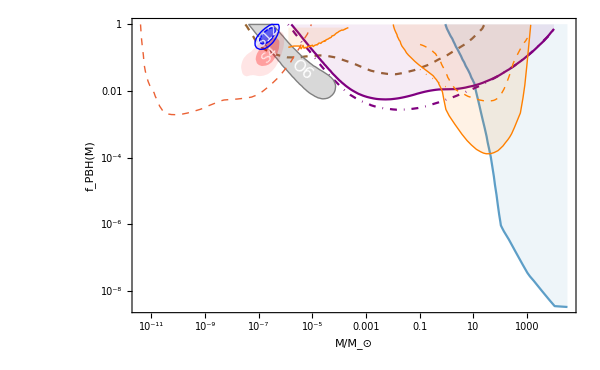

```mathematica
pbhcon=Show[eros3,disk2,ogle1,oglerelax,ogle3,hsc2,ligoasym,ligosgwb,ligomerger,ligosubsolar,s4,s12,PlotRange->Full]
```